# AOE Thin-Wall Project

Group 7 - Don’t call my name, Don’t call my name, Mariko. That’s not my name, That’s not my name, Thottman (Aesthetics), Vyon Coetzer, David Del Grosso, David Gardiner, Gaurav Sakhawala, Ronak Shah

```mathematica
ClearAll["Global`*"]
```

## Constants

```mathematica
ClearAll["Global`*"]
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.05443575 chord[x];*)(*box height (ft)*)
heightL[x_]=.05443575*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.05443575*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.05443575*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.05443575*chordR[x];*)
e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)
(*tcl[x_]=.001;
tcr[x_]=.005;*)
(*tL[x_]=tf*heightR[95.8]
tR[x_]=tf*heightR[95.8];*)
r = 0.25; (*radius of stringer ft*)
r2 = 0.25;
ASL=π*r^2;
ASR= Pi*r2^2;

Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+ρAl*ASL,{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+ρAl*ASR,{x,27.5,95.8}];(*weight of spar (lbz)*)

tL=tf*heightR[95.8];
tR=tf*heightR[95.8];
tf = 0.085



ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
(*IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)*)

IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL)*(heightL[x]-2tL)^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL)*(widthL[x]-2tL)^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR)*(heightR[x]-2tR)^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR)*(widthR[x]-2tR)^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)

Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS(*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
Leng = 20;
```

0.085

5.0087×10^6

## Case 1 (Takeoff)

Lift

```mathematica
(* distributed load *)
py[x_]=a x^2+b x+c;
Lift  = (1/2 )*ρ*Vto^2*S*clmax*e;
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Lift/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]];
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}]; (*total lift*)

PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL)*(heightL[x]-2tL)+ρAl*ASL;
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR)*(heightR[x]-2tR)+ρAl*ASR;

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-PyWL[x]),x]+c1a;
VyLM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c2a;
VyRM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c3a;
VyR[x_]=Integrate[-(py[x]-PyWR[x]),x]+c4a;

MzL[x_]=Integrate[-VyL[x],x]+c5a;
MzLM[x_]=Integrate[-VyLM[x],x]+c6a;
MzRM[x_]=Integrate[-VyRM[x],x]+c7a;
MzR[x_]=Integrate[-VyR[x],x]+c8a;


rotyL[x_]=Integrate[MzL[x]/(EE IzzL[x]),x]+c9a;
rotyLM[x_]=Integrate[MzLM[x]/(EE IzzL[x]),x]+c10a;
rotyRM[x_]=Integrate[MzRM[x]/(EE IzzL[x]),x]+c11a;
rotyR[x_]=Integrate[MzR[x]/(EE IzzR[x]),x]+c12a;

uyL[x_]=Integrate[rotyL[x],x]+c13a;
uyLM[x_]=Integrate[rotyLM[x],x]+c14a;
uyRM[x_]=Integrate[rotyRM[x],x]+c15a;
uyR[x_]=Integrate[rotyR[x],x]+c16a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyLM[Llg];
eq9a=rotyLM[Leng]==rotyRM[Leng];
eq10a=rotyRM[Ltaper]==rotyR[Ltaper];
eq11a=uyL[Llg]==uyLM[Llg];
eq12a=uyLM[Leng]==uyRM[Leng];
eq13a=uyRM[Ltaper]==uyR[Ltaper];
eq14a=MzL[Llg]==MzLM[Llg];
eq15a=MzLM[Leng]==MzRM[Leng];
eq16a=MzRM[Ltaper]==MzR[Ltaper];
eq17a=VyL[Llg]+Wlg==VyLM[Llg];
eq18a=VyLM[Leng]+Weng==VyRM[Leng];
eq19a=VyRM[Ltaper]== VyR[Ltaper];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a,eq16a,eq17a,eq18a,eq19a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a,c13a,c14a,c15a,c16a}];

c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];
c13a=c13a/.sol2a[[1]];
c14a=c14a/.sol2a[[1]];
c15a=c15a/.sol2a[[1]];
c16a=c16a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyLM[x_]=VyLM[x];
VyRM[x_]=VyRM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzLM[x_]=MzLM[x];
MzRM[x_]=MzRM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyLM[x_]=rotyLM[x];
rotyRM[x_]=rotyRM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyLM[x_]=uyLM[x];
uyRM[x_]=uyRM[x];
uyR[x_]=uyR[x];
```

Drag

```mathematica
pzL[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);
pzM[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);
pzR[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);

VzL[x_]=Integrate[-pzL[x],x]+c1b;
VzM[x_]=Integrate[-pzM[x],x]+c2b;
VzR[x_]=Integrate[-pzR[x],x]+c3b;

MyL[x_]=Integrate[VzL[x],x]+c4b;
MyM[x_]=Integrate[VzM[x],x]+c5b;
MyR[x_]=Integrate[VzR[x],x]+c6b;

rotzL[x_]=Integrate[-MyL[x]/(EE IyyL[x]),x]+c7b;
rotzM[x_]=Integrate[-MyM[x]/(EE IyyL[x]),x]+c8b;
rotzR[x_]=Integrate[-MyR[x]/(EE IyyR[x]),x]+c9b;

uzL[x_]=Integrate[rotzL[x],x]+c10b;
uzM[x_]=Integrate[rotzM[x],x]+c11b;
uzR[x_]=Integrate[rotzR[x],x]+c12b;

(*boundary and matching conditions*)
eq1b=VzR[Lw]==0;
eq2b=MyR[Lw]==0;
eq3b=rotzL[0]==0;
eq4b=uzL[0]==0;
eq5b=rotzL[Leng]==rotzM[Leng];
eq6b=rotzM[Ltaper]==rotzR[Ltaper];
eq7b=uzL[Leng]==uzM[Leng];
eq8b=uzM[Ltaper]==uzR[Ltaper];
eq9b=MyL[Leng]==MyM[Leng];
eq10b=MyM[Ltaper]==MyR[Ltaper];
eq11b=VzL[Leng]+T==VzM[Leng];
eq12b=VzM[Ltaper]==VzR[Leng];

(*solve for constants*)
sol1b=Solve[{eq1b,eq2b,eq3b,eq4b,eq5b,eq6b,eq7b,eq8b,eq9b,eq10b,eq11b,eq12b},{c1b,c2b,c3b,c4b,c5b,c6b,c7b,c8b,c9b,c10b,c11b,c12b}];
c1b=c1b/.sol1b[[1]];
c2b=c2b/.sol1b[[1]];
c3b=c3b/.sol1b[[1]];
c4b=c4b/.sol1b[[1]];
c5b=c5b/.sol1b[[1]];
c6b=c6b/.sol1b[[1]];
c7b=c7b/.sol1b[[1]];
c8b=c8b/.sol1b[[1]];
c9b=c9b/.sol1b[[1]];
c10b=c10b/.sol1b[[1]];
c11b=c11b/.sol1b[[1]];
c12b=c12b/.sol1b[[1]];

(*apply newfound constants*)
pzL[x_]=pzL[x];
pzM[x_]=pzM[x];
pzR[x_]=pzR[x];
VzL[x_]=VzL[x];
VzM[x_]=VzM[x];
VzR[x_]=VzR[x];
MyL[x_]=MyL[x];
MyM[x_]=MyM[x];
MyR[x_]=MyR[x];
rotzL[x_]=rotzL[x];
rotzM[x_]=rotzM[x];
rotzR[x_]=rotzR[x];
uzL[x_]=uzL[x];
uzM[x_]=uzM[x];
uzR[x_]=uzR[x];
```

Stress

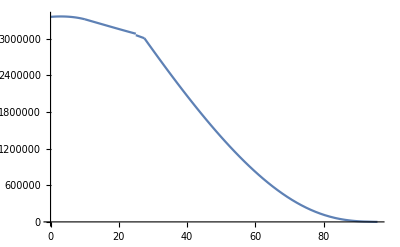

5.24031×10^6

```mathematica
σxxL[x_] =Abs[ (MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzL[x]*heightL[x]/2)/IzzL[x]]; (*0 < x < 10.06 (Llg)*) 
σxxM1[x_] = Abs[(MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzLM[x]*heightL[x]/2)/IzzL[x]]; (*10.06 < x < Leng*)
σxxM2[x_] = Abs[(MyM[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzRM[x]*heightL[x]/2)/IzzL[x]];(*Leng < x < 27.5*)
σxxR[x_] = Abs[(MyR[x]*-widthR[x]/2)/IyyR[x]]+Abs[(MzR[x]*heightR[x]/2)/IzzR[x]];(*27.5 < x < 95.8*)
Leng=25;
plt1 = Plot[σxxL[x],{x,0,10.06}];
plt2 = Plot[σxxM1[x],{x,10.06,Leng}];
plt3 = Plot[σxxM2[x],{x,Leng,27.5}];
plt4 = Plot[σxxR[x],{x,27.5,95.8}];

Show[{plt1,plt2,plt3,plt4},PlotRange->All,AxesOrigin->{0,0}]
σmax = σxxR[0]
```

```mathematica
(*num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,σxxM2[27.5,Leng]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]*)
```

```mathematica
Show[%8935,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress @ 27.5ft (max) vs Location of Engine Case 1"],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Real is not a type of graphics.

Show[0.75,AxesLabel→{Location of Engine (ft),Stress (Pa)},PlotLabel→Stress @ 27.5ft (max) vs Location of Engine Case 1,LabelStyle→{GrayLevel[0]}]

```mathematica
(*num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,uyR[Lw]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]*)
```

```mathematica
(*thick={height/4,height/8,height/12,height/15,height/20,height/25,height/50,height/100};
data1=Transpose@{thick,tipdeflection[Lw,20,thick]};
data2=Transpose@{thick,tipdeflection[Lw,(52.3+20)/2,thick]};
data3=Transpose@{thick,tipdeflection[Lw,52.3,thick]}*)
ListPlot[{data},PlotLabel->"Tip Deflection vs Engine Location Case 1",AxesLabel->{"Engine Location (ft)","Deflection (ft)"}]
```

-Graphics-

```mathematica
(*tf={height/4,height/8,height/20,height/50,height/100};
Leng=20;
dataL=Transpose@{t,σxxR[27.5]};
(*Leng=(52.3+20)/2;
dataM=Transpose@{tf,σxx};
Leng=52.3;
dataR=Transpose@{t,σxx};
ListPlot[{dataL,dataM,dataR},PlotLegends->{"Leftmost Engine","Central Engine","Rightmost Engine"}]*)
ListPlot[{dataL}]*)
```

## Constants

```mathematica
ClearAll["Global`*"]
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.05443575 chord[x];*)(*box height (ft)*)
heightL[x_]=.05443575*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.05443575*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.05443575*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.05443575*chordR[x];*)
e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)
(*tcl[x_]=.001;
tcr[x_]=.005;*)
(*tL[x_]=tf*heightR[95.8]
tR[x_]=tf*heightR[95.8];*)
Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]),{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]),{x,27.5,95.8}];(*weight of spar (lbz)*)

tL=tf*heightR[95.8];
tR=tf*heightR[95.8];
tf = 0.095;

r = 0.25; (*radius of stringer ft*)
r2 = 0.25;
ASL=π*r^2;
ASR= Pi*r2^2;

ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
(*IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)*)

IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL)*(heightL[x]-2tL)^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL)*(widthL[x]-2tL)^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR)*(heightR[x]-2tR)^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR)*(widthR[x]-2tR)^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)

Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS;(*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
Leng = 20;
```

## Case 2 (Engine Failure)

Lift

```mathematica
(* distributed load *)
py[x_]=a x^2+b x+c;
Lift  = (1/2 )*ρ*Vto^2*S*clmax*e;
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Lift/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]]; 
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}]; (*total lift*)

PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL)*(heightL[x]-2tL);
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR)*(heightR[x]-2tR);

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-PyWL[x]),x]+c1a;
VyLM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c2a;
VyRM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c3a;
VyR[x_]=Integrate[-(py[x]-PyWR[x]),x]+c4a;

MzL[x_]=Integrate[-VyL[x],x]+c5a;
MzLM[x_]=Integrate[-VyLM[x],x]+c6a;
MzRM[x_]=Integrate[-VyRM[x],x]+c7a;
MzR[x_]=Integrate[-VyR[x],x]+c8a;

rotyL[x_]=Integrate[MzL[x]/(EE IzzL[x]),x]+c9a;
rotyLM[x_]=Integrate[MzLM[x]/(EE IzzL[x]),x]+c10a;
rotyRM[x_]=Integrate[MzRM[x]/(EE IzzL[x]),x]+c11a;
rotyR[x_]=Integrate[MzR[x]/(EE IzzR[x]),x]+c12a;

uyL[x_]=Integrate[rotyL[x],x]+c13a;
uyLM[x_]=Integrate[rotyLM[x],x]+c14a;
uyRM[x_]=Integrate[rotyRM[x],x]+c15a;
uyR[x_]=Integrate[rotyR[x],x]+c16a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyLM[Llg];
eq9a=rotyLM[Leng]==rotyRM[Leng];
eq10a=rotyRM[Ltaper]==rotyR[Ltaper];
eq11a=uyL[Llg]==uyLM[Llg];
eq12a=uyLM[Leng]==uyRM[Leng];
eq13a=uyRM[Ltaper]==uyR[Ltaper];
eq14a=MzL[Llg]==MzLM[Llg];
eq15a=MzLM[Leng]==MzRM[Leng];
eq16a=MzRM[Ltaper]==MzR[Ltaper];
eq17a=VyL[Llg]+Wlg==VyLM[Llg];
eq18a=VyLM[Leng]+Weng==VyRM[Leng];
eq19a=VyRM[Ltaper]== VyR[Ltaper];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a,eq16a,eq17a,eq18a,eq19a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a,c13a,c14a,c15a,c16a}];

c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];
c13a=c13a/.sol2a[[1]];
c14a=c14a/.sol2a[[1]];
c15a=c15a/.sol2a[[1]];
c16a=c16a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyLM[x_]=VyLM[x];
VyRM[x_]=VyRM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzLM[x_]=MzLM[x];
MzRM[x_]=MzRM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyLM[x_]=rotyLM[x];
rotyRM[x_]=rotyRM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyLM[x_]=uyLM[x];
uyRM[x_]=uyRM[x];
uyR[x_]=uyR[x]



num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,uyR[Lw]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]
```

(-1.11008×10^49-3.15252×10^16 ⅈ)+(6.79769×10^31+5.25232×10^30 ⅈ) x-4.99302×10^12 x^2+(17988.3+0. ⅈ) Log[139.095-1. x]+(2137.01+0. ⅈ) Log[140.466-1. x]-(2539.37+0. ⅈ) Log[182.342-1. x]+(2.79905×10^47+0. ⅈ) Log[1.6742×10^17-1. x]-(1.67187×10^30+0. ⅈ) x Log[-1.6742×10^17+x]+(13.9264+0. ⅈ) x Log[-182.342+x]-(15.2137+0. ⅈ) x Log[-140.466+x]-(129.324+0. ⅈ) x Log[-139.095+x]

-Graphics-

```mathematica
Show[%8017,AxesLabel->{HoldForm[Location of Engine ft],HoldForm[Deflection ft]},PlotLabel->HoldForm[Tip Deflection ft vs Location of Engine ft Case 2],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Times is not a type of graphics.

Show[0.65 (38.94-0.507636 x),AxesLabel→{Location of Engine ft,Deflection ft},PlotLabel→Tip Deflection ft vs Location of Engine ft Case 2,LabelStyle→{GrayLevel[0]}]

Drag

```mathematica
pzL[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);
pzM[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);
pzR[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);

VzL[x_]=Integrate[-pzL[x],x]+c1b;
VzM[x_]=Integrate[-pzM[x],x]+c2b;
VzR[x_]=Integrate[-pzR[x],x]+c3b;

MyL[x_]=Integrate[VzL[x],x]+c4b;
MyM[x_]=Integrate[VzM[x],x]+c5b;
MyR[x_]=Integrate[VzR[x],x]+c6b;

rotzL[x_]=Integrate[-MyL[x]/(EE IyyL[x]),x]+c7b;
rotzM[x_]=Integrate[-MyM[x]/(EE IyyL[x]),x]+c8b;
rotzR[x_]=Integrate[-MyR[x]/(EE IyyR[x]),x]+c9b;

uzL[x_]=Integrate[rotzL[x],x]+c10b;
uzM[x_]=Integrate[rotzM[x],x]+c11b;
uzR[x_]=Integrate[rotzR[x],x]+c12b;

(*boundary and matching conditions*)
eq1b=VzR[Lw]==0;
eq2b=MyR[Lw]==0;
eq3b=rotzL[0]==0;
eq4b=uzL[0]==0;
eq5b=rotzL[Leng]==rotzM[Leng];
eq6b=rotzM[Ltaper]==rotzR[Ltaper];
eq7b=uzL[Leng]==uzM[Leng];
eq8b=uzM[Ltaper]==uzR[Ltaper];
eq9b=MyL[Leng]==MyM[Leng];
eq10b=MyM[Ltaper]==MyR[Ltaper];
eq11b=VzL[Leng]+T==VzM[Leng];
eq12b=VzM[Ltaper]==VzR[Leng];

(*solve for constants*)
sol1b=Solve[{eq1b,eq2b,eq3b,eq4b,eq5b,eq6b,eq7b,eq8b,eq9b,eq10b,eq11b,eq12b},{c1b,c2b,c3b,c4b,c5b,c6b,c7b,c8b,c9b,c10b,c11b,c12b}];
c1b=c1b/.sol1b[[1]];
c2b=c2b/.sol1b[[1]];
c3b=c3b/.sol1b[[1]];
c4b=c4b/.sol1b[[1]];
c5b=c5b/.sol1b[[1]];
c6b=c6b/.sol1b[[1]];
c7b=c7b/.sol1b[[1]];
c8b=c8b/.sol1b[[1]];
c9b=c9b/.sol1b[[1]];
c10b=c10b/.sol1b[[1]];
c11b=c11b/.sol1b[[1]];
c12b=c12b/.sol1b[[1]];

(*apply newfound constants*)
pzL[x_]=pzL[x];
pzM[x_]=pzM[x];
pzR[x_]=pzR[x];
VzL[x_]=VzL[x];
VzM[x_]=VzM[x];
VzR[x_]=VzR[x];
MyL[x_]=MyL[x];
MyM[x_]=MyM[x];
MyR[x_]=MyR[x];
rotzL[x_]=rotzL[x];
rotzM[x_]=rotzM[x];
rotzR[x_]=rotzR[x];
uzL[x_]=uzL[x];
uzM[x_]=uzM[x];
uzR[x_]=uzR[x];
```

Stress

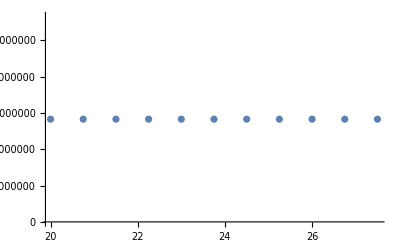

```mathematica
σxxL[x_,Leng_] =Abs[ (MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzL[x]*heightL[x]/2)/IzzL[x]]; (*0 < x < 10.06 (Llg)*) 
σxxM1[x_,Leng_] = Abs[(MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzLM[x]*heightL[x]/2)/IzzL[x]]; (*10.06 < x < Leng*)
σxxM2[x_,Leng_] = Abs[(MyM[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzRM[x]*heightL[x]/2)/IzzL[x]];(*Leng < x < 27.5*)
σxxR[x_,Leng_] = Abs[(MyR[x]*-widthR[x]/2)/IyyR[x]]+Abs[(MzR[x]*heightR[x]/2)/IzzR[x]];(*27.5 < x < 95.8*)

(*plt1 = Plot[σxxL[x,Leng],{x,0,10.06}];
plt2 = Plot[σxxM1[x,Leng],{x,10.06,Leng}];
plt3 = Plot[σxxM2[x,Leng],{x,Leng,27.5}];
plt4 = Plot[σxxR[x,Leng],{x,27.5,95.8}];

Show[{plt1,plt2,plt3,plt4},PlotRange->All,AxesOrigin->{0,0}];*)

num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,σxxM2[27.5,Leng]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]
```

```mathematica
Show[%8086,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress at 27.5ft Max vs Engine Location Case 2"],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Complex is not a type of graphics.

Show[-9.93276+5.93834×10^-13 ⅈ,AxesLabel→{Location of Engine (ft),Stress (Pa)},PlotLabel→Stress at 27.5ft Max vs Engine Location Case 2,LabelStyle→{GrayLevel[0]}]

```mathematica
maxLeng=Solve[T*(Leng+Rfuse)== 5390000/FS,Leng];
maxLeng=Leng/.maxLeng[[1]];
```

Solve::ivar: 20 is not a valid variable.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

## Constants

```mathematica
ClearAll["Global`*"]
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.05443575 chord[x];*)(*box height (ft)*)
heightL[x_]=.05443575*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.05443575*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.05443575*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.05443575*chordR[x];*)
e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)
(*tcl[x_]=.001;
tcr[x_]=.005;*)
(*tL[x_]=tf*heightR[95.8]
tR[x_]=tf*heightR[95.8];*)
Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]),{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]),{x,27.5,95.8}];(*weight of spar (lbz)*)

tL=tf*heightR[95.8];
tR=tf*heightR[95.8];
tf = 0.11;

r = 0.25; (*radius of stringer ft*)
r2 = 0.25;
ASL=π*r^2;
ASR= Pi*r2^2;

ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
(*IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)*)

IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL)*(heightL[x]-2tL)^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL)*(widthL[x]-2tL)^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR)*(heightR[x]-2tR)^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR)*(widthR[x]-2tR)^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)

Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS;(*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
Leng = 20;
```

## Case 3 (Static)

```mathematica
a=17.58; b=22.85; c=53.27; d=74.63;
 e=93.18; f=118.32; g=144.42; h=156.11;
sol3a=Solve[0== -Wto*(67)+2*Flg*(e-a),Flg]
Flg=Flg/.sol3a[[1]];
```

{{Flg→243717.}}

```mathematica
(* distributed load *)
py[x_]=0;
PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL)*(heightL[x]-2tL);
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR)*(heightR[x]-2tR);

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-PyWL[x]),x]+c1a;
VyLM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c2a;
VyRM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c3a;
VyR[x_]=Integrate[-(py[x]-PyWR[x]),x]+c4a;

MzL[x_]=Integrate[-VyL[x],x]+c5a;
MzLM[x_]=Integrate[-VyLM[x],x]+c6a;
MzRM[x_]=Integrate[-VyRM[x],x]+c7a;
MzR[x_]=Integrate[-VyR[x],x]+c8a;

rotyL[x_]=Integrate[MzL[x]/(EE IzzL[x]),x]+c9a;
rotyLM[x_]=Integrate[MzLM[x]/(EE IzzL[x]),x]+c10a;
rotyRM[x_]=Integrate[MzRM[x]/(EE IzzL[x]),x]+c11a;
rotyR[x_]=Integrate[MzR[x]/(EE IzzR[x]),x]+c12a;

uyL[x_]=Integrate[rotyL[x],x]+c13a;
uyLM[x_]=Integrate[rotyLM[x],x]+c14a;
uyRM[x_]=Integrate[rotyRM[x],x]+c15a
uyR[x_]=Integrate[rotyR[x],x]+c16a

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyLM[Llg];
eq9a=rotyLM[Leng]==rotyRM[Leng];
eq10a=rotyRM[Ltaper]==rotyR[Ltaper];
eq11a=uyL[Llg]==uyLM[Llg];
eq12a=uyLM[Leng]==uyRM[Leng];
eq13a=uyRM[Ltaper]==uyR[Ltaper];
eq14a=MzL[Llg]==MzLM[Llg];
eq15a=MzLM[Leng]==MzRM[Leng];
eq16a=MzRM[Ltaper]==MzR[Ltaper];
eq17a=VyL[Llg]+Wlg==VyLM[Llg]+Flg;
eq18a=VyLM[Leng]+Weng==VyRM[Leng];
eq19a=VyRM[Ltaper]== VyR[Ltaper];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a,eq16a,eq17a,eq18a,eq19a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a,c13a,c14a,c15a,c16a}];

c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];
c13a=c13a/.sol2a[[1]]
c14a=c14a/.sol2a[[1]];
c15a=c15a/.sol2a[[1]]
c16a=c16a/.sol2a[[1]]

VyL[x_]=VyL[x];
VyLM[x_]=VyLM[x];
VyRM[x_]=VyRM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzLM[x_]=MzLM[x];
MzRM[x_]=MzRM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyLM[x_]=rotyLM[x];
rotyRM[x_]=rotyRM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyLM[x_]=uyLM[x];
uyRM[x_]=uyRM[x];
uyR[x_]=uyR[x]
uyR[95]
MzR[95.8]

num=(27.5-20)/10;
(*uvec={};Do[AppendTo[uvec,uyR[Leng ]],{Leng,20,27.5,num}]
data1=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data1] (*deflection at Leng*);*)


(*uvec2={};Do[AppendTo[uvec2,uyR[Lw]],{Leng,20,27.5,num}];
data2=Transpose@{Range[20,27.5,num],uvec2};
ListPlot[data2] (*deflection at Lw*)*)





(*thick={height/4,height/8,height/12,height/15,height/20,height/25,height/50,height/100};
data1=Transpose@{thick,tipdeflection[Lw,20,thick]}
data2=Transpose@{thick,tipdeflection[Lw,(52.3+20)/2,thick]};
data3=Transpose@{thick,tipdeflection[Lw,52.3,thick]};
ListPlot[{data1,data2,data3},PlotLegends->{"Leftmost Engine","Central Engine","Rightmost Engine"},PlotLabel->"Tip Deflection",AxesLabel->{"Thickness (ft)","Deflection (ft)"}]*)
```

c15a+0.00177378 x+c11a x-2.80731×10^-14 c3a x+3.64924×10^-16 c7a x-0.0000541448 x^2-2.77998×10^-22 x^3-550.606 Log[76.5105-1. x]-0.0392473 c3a Log[76.5105-1. x]+0.000512966 c7a Log[76.5105-1. x]+602.209 Log[77.4006-1. x]+0.0426808 c3a Log[77.4006-1. x]-0.000551427 c7a Log[77.4006-1. x]-53.3359 Log[91.6157-1. x]-0.00352368 c3a Log[91.6157-1. x]+0.0000384615 c7a Log[91.6157-1. x]+0.58217 x Log[-91.6157+x]+0.0000384615 c3a x Log[-91.6157+x]-4.19814×10^-7 c7a x Log[-91.6157+x]-7.78042 x Log[-77.4006+x]-0.000551427 c3a x Log[-77.4006+x]+7.12433×10^-6 c7a x Log[-77.4006+x]+7.19647 x Log[-76.5105+x]+0.000512966 c3a x Log[-76.5105+x]-6.70452×10^-6 c7a x Log[-76.5105+x]

c16a-1.08653×10^14 x+c12a x-3.72406×10^-14 c4a x+2.66051×10^-16 c8a x-5994.43 Log[139.001-1. x]-0.294707 c4a Log[139.001-1. x]+0.00212018 c8a Log[139.001-1. x]+6603.64 Log[141.026-1. x]+0.322351 c4a Log[141.026-1. x]-0.00228576 c8a Log[141.026-1. x]-637.936 Log[173.366-1. x]-0.0287059 c4a Log[173.366-1. x]+0.00016558 c8a Log[173.366-1. x]-2.10629×10^31 Log[1.93855×10^17-1. x]+0.00106145 c4a Log[1.93855×10^17-1. x]-5.47547×10^-21 c8a Log[1.93855×10^17-1. x]+1.08653×10^14 x Log[-1.93855×10^17+x]-5.47547×10^-21 c4a x Log[-1.93855×10^17+x]+2.82452×10^-38 c8a x Log[-1.93855×10^17+x]+3.67972 x Log[-173.366+x]+0.00016558 c4a x Log[-173.366+x]-9.55092×10^-7 c8a x Log[-173.366+x]-46.8258 x Log[-141.026+x]-0.00228576 c4a x Log[-141.026+x]+0.0000162081 c8a x Log[-141.026+x]+43.1252 x Log[-139.001+x]+0.00212018 c4a x Log[-139.001+x]-0.000015253 c8a x Log[-139.001+x]

466.878+0. ⅈ

-4.71775+5.34866×10^-13 ⅈ

8.38428×10^32+1.29236 ⅈ

(8.38428×10^32+1.29236 ⅈ)-(4.43367×10^15+3.41343×10^14 ⅈ) x-(178.697+0. ⅈ) Log[139.001-1. x]+(206.138+0. ⅈ) Log[141.026-1. x]-(26.9123+0. ⅈ) Log[173.366-1. x]-(2.10629×10^31+0. ⅈ) Log[1.93855×10^17-1. x]+(1.08653×10^14+0. ⅈ) x Log[-1.93855×10^17+x]+(0.155235+0. ⅈ) x Log[-173.366+x]-(1.4617+0. ⅈ) x Log[-141.026+x]+(1.28558+0. ⅈ) x Log[-139.001+x]

0.+0. ⅈ

2.32831×10^-10+0. ⅈ

```mathematica
Show[%8772,AxesLabel->{HoldForm[Location of Engine ft],HoldForm[Tip Deflection ft]},PlotLabel->HoldForm[Tip Deflection vs Location of Engine Case 3],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Symbol is not a type of graphics.

Show[Null,AxesLabel→{Location of Engine ft,Tip Deflection ft},PlotLabel→Tip Deflection vs Location of Engine Case 3,LabelStyle→{GrayLevel[0]}]

```mathematica
{{0.13248300656249998,-23.08462321638492},{0.06624150328124999,-11.603174462498314},{0.021197281049999996,11.884766836036333},{0.010598640524999998,41.998900299869774},{0.005299320262499999,101.14113311866477}}
```

{{0.132483,-23.0846},{0.0662415,-11.6032},{0.0211973,11.8848},{0.0105986,41.9989},{0.00529932,101.141}}

```mathematica
σxxL[x_] =Abs[(MzL[x]*heightL[x]/2)/IzzL[x]]; (*0 < x < 10.06 (Llg)*) 
σxxM1[x_] =Abs[(MzLM[x]*heightL[x]/2)/IzzL[x]]; (*10.06 < x < Leng*)
σxxM2[x_] = Abs[(MzRM[x]*heightL[x]/2)/IzzL[x]];(*Leng < x < 27.5*)
σxxR[x_] = Abs[(MzR[x]*heightR[x]/2)/IzzR[x]];(*27.5 < x < 95.8*)


num=(27.5-20)/10;
(*uvec3={};Do[AppendTo[uvec3,Abs[σxxM2[27.5,Leng]]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec3};
ListPlot[data]*)
```

```mathematica
Show[%8776,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress @ 27.5ft along Spar (max) vs Engine Location Case 3"],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Times is not a type of graphics.

Show[0.0544358 (38.94-0.507636 x),AxesLabel→{Location of Engine (ft),Stress (Pa)},PlotLabel→Stress @ 27.5ft along Spar (max) vs Engine Location Case 3,LabelStyle→{GrayLevel[0]}]

```mathematica
````
```